```mathematica
Thermometer ID:Ali Fake T 2
Type:Polynomial
Info:X type:R (ohm)
Y type:T (K)
x0:10000
y0:1
xmin:1000
xmax:100000
Polynomial coefficients:X scaling:log10(x/x0)
Y scaling:log10(y/y0)
{0.2106,
-1.9547183805737,
0.70744760503859,
-0.14805728518745,
-0.15153669415591,
0.13143244734904,
-0.027637396733984}
```

```mathematica
tt1 ={0.2106,
-1.9547183805737,
0.70744760503859,
-0.14805728518745,
-0.15153669415591,
0.13143244734904,
-0.027637396733984};
```

```mathematica
10^(Sum[ x^(n-1)tt1[[n]], {n, 1, Length[tt1]}]/.x-> Log10[R/10000])
```

```mathematica
tt1 ={0.2106,
-1.9547183805737,
0.70744760503859,
-0.14805728518745,
-0.15153669415591,
0.13143244734904,
-0.027637396733984};
```

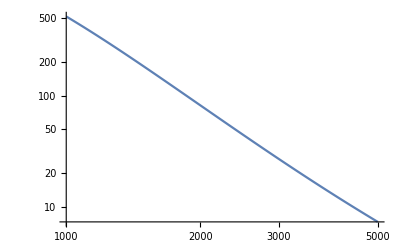

```mathematica
LogLogPlot[ 10^(Sum[ x^(n-1)tt1[[n]], {n, 1, Length[tt1]}]/.x-> Log10[R/10000]), {R,1000, 5000}]
```

```mathematica
10^(Sum[ x^(n-1)tt1[[n]], {n, 1, Length[tt1]}]/.x-> Log10[R/10000])/.R-> 4581
```

9.07369

```mathematica
10^(Sum[ x^(n-1)tt1[[n]], {n, 1, Length[tt1]}]/.x-> Log10[R/10000])/.R-> 1250
```

293.204

```mathematica
(Log10[10^((a+ b x)/.x-> Log10[R/10000])/.R-> 4581 ]//N) == Log10[1.6/9.07] //N
```

0.434294 Log[10.^(a-0.33904 b)]==-0.753487

```mathematica
0.43429448190325176(a-0.3390397082239163 b)==-0.7534873044041704
```

```mathematica
(Log10[10^((a+ b x)/.x-> Log10[R/10000])/.R-> 1250 ]//N) == Log10[1] //N
```

0.434294 Log[10.^(a-0.90309 b)]==0.

```mathematica
0.43429448190325176 (a-0.9030899869919433 b)==0.
```

```mathematica
Solve[ { 0.43429448190325176 (a-0.9030899869919433 b)==0.,0.43429448190325176(a-0.3390397082239163 b)==-0.7534873044041704},{a,b}]
```

```mathematica
tt1[[1]]
```

0.2106

```mathematica
LinguisticAssistant
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\data\nanocal-Mar2020

```mathematica
t111= Import[ "C002 and C003Th1.txt", "Table"][[All,{1,2}]]//keep[ #[[1]]>0 && #[[2]]>0 &]; 
maxt111 = Max[t111[[All,1]]];
mint111 = Min[t111[[All,1]]];

t11 = t111 // map2[ {298/(maxt111-mint111)  #[[1]], #[[2]]}&]; 
t1=t11// map2[ {Log10[ (#[[2]])/10000 ]  , Log10[#[[1]] ]}&]//sdecimate[1000];
t1d=t11// map2[ {Log10[ (#[[2]])/10000 ]  , Log10[#[[1]] ]}&]//sdecimate[20];
```

```mathematica
t222= Import[ "C002 and C003Th2.txt", "Table"][[All,{1,2}]]//keep[ #[[1]]>0 && #[[2]]>0 &]; 
maxt222 = Max[t222[[All,1]]];
mint222 = Min[t222[[All,1]]];

t22 = t222 // map2[ {298/(maxt222-mint222)  #[[1]], #[[2]]}&]; 
t2=t22// map2[ {Log10[ (#[[2]])/10000 ]  , Log10[#[[1]] ]}&]//sdecimate[1000];
t2d=t22// map2[ {Log10[ (#[[2]])/10000 ]  , Log10[#[[1]] ]}&]//sdecimate[30];

t2extra = ({{1.46, 6848}, {1.53, 6745}, {1.62, 6619}, {1.99, 6243}, {2.30, 5977}, {2.56, 5763}, {2.78, 5586}, {3.16, 5335}, {3.36, 5166}, {3.64, 5010}});(* FUDGE !!!*) t2extra = ({{1.46, 6848}, {1.53, 6745}, {1.62, 6619}, {1.99, 6243}, {2.30, 5977}, {2.56, 5763}, {2.98, 5586}, {3.86, 5335}, {4.2, 5166}, {4.5, 5010}});
t2extra2 =t2extra// map2[ {Log10[ (#[[2]])/10000 ]  , Log10[#[[1]] ]}&];
t2extra2max = Min[ t2extra2[[All,1]]];

t2merge =Join[ (t2d//keep[ #[[1]]<t2extra2max&] )//N, t2extra2//N];
```

```mathematica
t2merge
```

{{-0.866487,2.47687},{-0.843911,2.44961},{-0.821336,2.39258},{-0.798761,2.33451},{-0.776186,2.27335},{-0.753611,2.20833},{-0.731035,2.13982},{-0.70846,2.06604},{-0.685885,1.98855},{-0.66331,1.90679},{-0.640734,1.82494},{-0.618159,1.74174},{-0.595584,1.6556},{-0.573009,1.57474},{-0.550434,1.49247},{-0.527858,1.41042},{-0.505283,1.32941},{-0.482708,1.24877},{-0.460133,1.17355},{-0.437557,1.09564},{-0.414982,1.01928},{-0.392407,0.947329},{-0.369832,0.876327},{-0.347257,0.805692},{-0.324681,0.736543},{-0.302106,0.664558},{-0.164436,0.164353},{-0.171018,0.184691},{-0.179208,0.209515},{-0.204607,0.298853},{-0.223517,0.361728},{-0.239351,0.40824},{-0.252899,0.474216},{-0.272866,0.586587},{-0.286846,0.623249},{-0.300162,0.653213}}

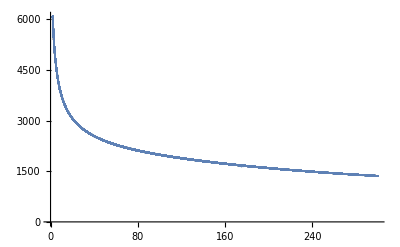

```mathematica
ListPlot[t11, PlotRange->All]
```

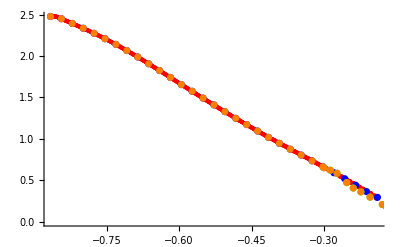

```mathematica
{ListPlot[t2, PlotStyle->Red],
ListPlot[t2d, PlotStyle->Blue], 
ListPlot[t2extra2, PlotStyle->Green] ,
ListPlot[t2merge, PlotStyle->Orange]

}//Show
```

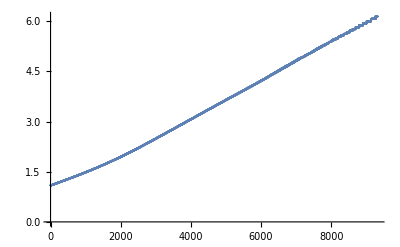

```mathematica
ListPlot[t2[[All,2]]]
```

```mathematica
ave[nx_,ny_, arr_]:= 1/Length[arr]∑_(n=1)^Length[arr] arr[[n,1]]^nx arr[[n,2]]^ny ;
ave[nx_,ny_]:= ave[nx,ny, #]&;
```

```mathematica
aaa = ({{ave, □, □, □, □, □}, {□, □, □, □, □, □}, {□, □, □, □, □, □}, {□, □, □, □, □, □}, {□, □, □, □, □, □}, {□, □, □, □, □, □}})
```

```mathematica
ma = Table[ ave[nx+ny-2,0],{nx, 1, 6}, {ny, 1, 6}] ; ma//MatrixForm
```

(ave[0,0,#1]& | ave[1,0,#1]& | ave[2,0,#1]& | ave[3,0,#1]& | ave[4,0,#1]& | ave[5,0,#1]&
ave[1,0,#1]& | ave[2,0,#1]& | ave[3,0,#1]& | ave[4,0,#1]& | ave[5,0,#1]& | ave[6,0,#1]&
ave[2,0,#1]& | ave[3,0,#1]& | ave[4,0,#1]& | ave[5,0,#1]& | ave[6,0,#1]& | ave[7,0,#1]&
ave[3,0,#1]& | ave[4,0,#1]& | ave[5,0,#1]& | ave[6,0,#1]& | ave[7,0,#1]& | ave[8,0,#1]&
ave[4,0,#1]& | ave[5,0,#1]& | ave[6,0,#1]& | ave[7,0,#1]& | ave[8,0,#1]& | ave[9,0,#1]&
ave[5,0,#1]& | ave[6,0,#1]& | ave[7,0,#1]& | ave[8,0,#1]& | ave[9,0,#1]& | ave[10,0,#1]&)

```mathematica
ma1 =  Table[ ave[nx+ny-2,0,t1],{nx, 1, 6}, {ny, 1, 6}] ; ma1//MatrixForm
ve1 = Table[ ave[nx-1,1,t1],{nx, 1, 6}] ; ve1//MatrixForm
a1 = Inverse[ ma1].ve1 ; a1 //MatrixForm
p1 = Sum[ a1[[n]] x^(n-1), {n, 1, Length[a1]}]
```

```mathematica
ma2=  Table[ ave[nx+ny-2,0,t2merge],{nx, 1, 6}, {ny, 1, 6}] ; ma2//MatrixForm
ve2 = Table[ ave[nx-1,1,t2merge],{nx, 1, 6}] ; ve2//MatrixForm
a2= Inverse[ ma2].ve2 ; a2//MatrixForm
p2= Sum[ a2[[n]] x^(n-1), {n, 1, Length[a2]}]
```

(1. | -0.485739 | 0.282503 | -0.184133 | 0.128619 | -0.0938533
-0.485739 | 0.282503 | -0.184133 | 0.128619 | -0.0938533 | 0.0705296
0.282503 | -0.184133 | 0.128619 | -0.0938533 | 0.0705296 | -0.0541318
-0.184133 | 0.128619 | -0.0938533 | 0.0705296 | -0.0541318 | 0.0422122
0.128619 | -0.0938533 | 0.0705296 | -0.0541318 | 0.0422122 | -0.0333294
-0.0938533 | 0.0705296 | -0.0541318 | 0.0422122 | -0.0333294 | 0.026581)

(1.27217
-0.77645
0.518631
-0.36685
0.269506
-0.203304)

(-0.676736
-6.17077
-8.01191
-5.95641
6.32597
7.41048)

-0.676736-6.17077 x-8.01191 x^2-5.95641 x^3+6.32597 x^4+7.41048 x^5

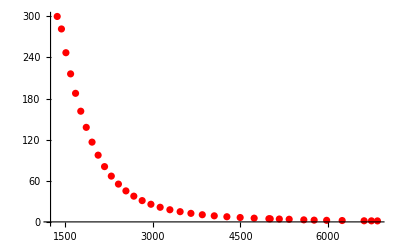

```mathematica
ListPlot[(t2merge//map2[ { 10000 10^(#[[1]]),10^(#[[2]])}&]), PlotStyle->Red]
```

```mathematica
p1
```

-1.42476-14.0399 x-42.0006 x^2-75.3411 x^3-60.9517 x^4-17.6265 x^5

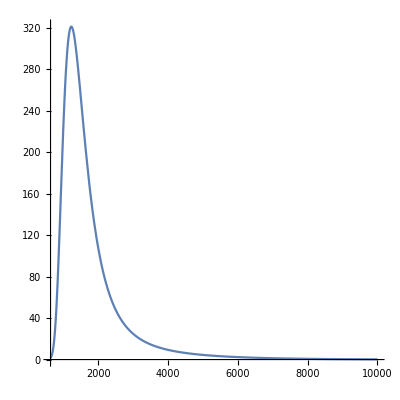

```mathematica
ParametricPlot[ {10000 10^x,10^p2}, {x, -1.2,0}, PlotRange->All, AspectRatio->1]
```

```mathematica
p1
```

-1.42476-14.0399 x-42.0006 x^2-75.3411 x^3-60.9517 x^4-17.6265 x^5

```mathematica
{10000 10^x,10^p1}/.x-> Log10[ 7330/10000]
```

{7330,0.742042}

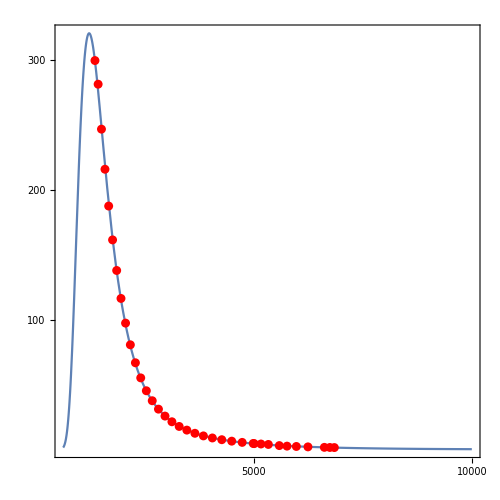

```mathematica
{
ParametricPlot[ {10000 10^x,10^p2}, {x, -1.2,0}, PlotRange->All, AspectRatio->1],
ListPlot[(t2merge//map2[ { 10000 10^(#[[1]]),10^(#[[2]])}&]), PlotStyle->Red] 
}//Show//nice//show[
PlotRange->All]
```

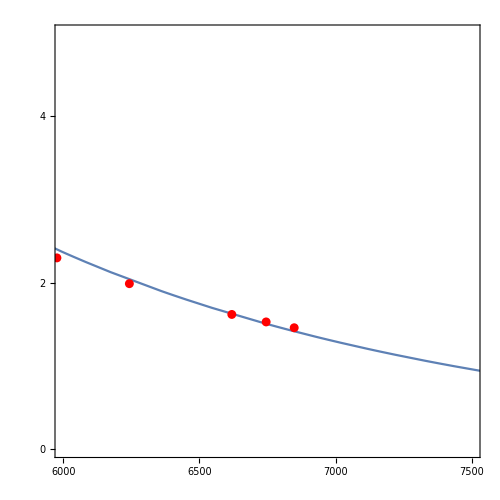

```mathematica
{
ParametricPlot[ {10000 10^x,10^p2}, {x, -1.2,0}, PlotRange->All, AspectRatio->1],
ListPlot[(t2merge//map2[ { 10000 10^(#[[1]]),10^(#[[2]])}&]), PlotStyle->Red] 
}//Show//nice//show[
PlotRange->{ { 6000, 7500}, {0,5}}]
```

```mathematica
a2//MatrixForm
```

(-0.676736
-6.17077
-8.01191
-5.95641
6.32597
7.41048)